```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/rex/Desktop/NEW

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
LECsNUCL=Import["/home/rex/Downloads/LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
```

```mathematica
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=3 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]

λRange=Range[1,Length[activeLEC]];
```

ℏ^2/(2  μ) = 13.8237

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
NormTT[core_?ArrayQ]:=Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^4/(3^2 ((core[[i]][[2]]+core[[j]][[2]])^2 (core[[k]][[2]]+core[[l]][[2]])^2)))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta1,eta2,eta3,w1,w2,w3},
eta2= 3^(7/2)Cc /(((Aa+Bb)(Gg+Hh)(2 lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2 lam+3Gg+3Hh)))^(3/2));
w2= 3(Aa+Bb)(Gg+Hh)lam/(2lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2lam+3Gg+3Hh));
eta3 =3^(7/2)Dd /(((Aa+Bb)(lam+Gg+Hh)(lam Bb+Gg(4lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh)))^(3/2));
w3 = 6(Aa+Bb)(Gg+Hh)lam/(lam Bb+Gg(4 lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh));
eta1 =3^(7/2)Dd /(((Gg+Hh)(4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))))^(3/2));
w1=(3(Aa+Bb)lam(Aa+Bb+2lam)(Gg+Hh))/((4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta1 Exp[-w1 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,-Graphics3D-Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=0;
a1=4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh;
b1=2Gg Bb -Gg Hh -2 Aa Bb +2 Aa Hh;
c1=Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh;

zeta2=0;
zeta3=0;

a2=4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh);
b2=Gg(4lam+2Bb-2 Hh)+Aa(-4lam-2Bb+2Gg);
c2=Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh);

a3= 4Bb(2lam+Hh)+Gg(Aa+2lam+Hh)+Aa(2lam+Bb+Hh);
b3=Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb);
c3=Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh);

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1./NormTT[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1;

Wmatt=ParallelTable[
cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;
DiagonalMatrix[Table[-cij hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]]
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmatt,4];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
(*Print[(Chop[Wmat])[[1;;4,1;;4]]//MatrixForm];*)
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
(*Print["N_terms = ",Length[a00]^4," calculated for E_rel = ",energyMeV," MeV"];*)
tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_]:=Module[{locall=l},

dataS={};
tanDsL={};
tanDs={};

eRange=Range[0.01,0.1,0.03];

LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];

SetSharedVariable[tanDs];

Do[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
,{energ,eRange}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)

(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 eRange],Sqrt[mh2 eRange ]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦1;;3⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
{a0tf,r0tf,dataS}
]
```

```mathematica
JacobiWavefunctions={
{10.0,{{10.00000000,31.99411600,28.09173000},{10.00000000,31.99411600,1.98675000},{10.00000000,31.99411600,0.48037900},{10.00000000,31.99411600,0.09885800},{10.00000000,31.92980200,28.09173000},{10.00000000,31.92980200,1.98675000},{10.00000000,31.92980200,0.48037900},{10.00000000,31.92980200,0.09885800},{69.00000000,8.62287600,28.09173000},{-500.00000000,8.62287600,1.98675000},{-963.00000000,8.62287600,0.48037900},{-413.00000000,8.62287600,0.09885800},{-318.00000000,1.85449700,28.09173000},{10.00000000,1.85449700,1.98675000},{10.00000000,1.85449700,0.48037900},{10.00000000,1.85449700,0.09885800},{319.00000000,1.55352400,28.09173000},{541.00000000,1.55352400,1.98675000},{10.00000000,1.55352400,0.48037900},{10.00000000,1.55352400,0.09885800},{-39.00000000,0.74605000,28.09173000},{-148.00000000,0.74605000,1.98675000},{-768.00000000,0.74605000,0.48037900},{10.00000000,0.74605000,0.09885800},{1.00000000,0.03753000,28.09173000},{-7.00000000,0.03753000,1.98675000},{45.00000000,0.03753000,0.48037900},{-597.00000000,0.03753000,0.09885800},{34.00000000,78.47769200,1.85924700},{39.00000000,78.47769200,0.59372200},{36.00000000,78.47769200,0.15929400},{438.00000000,30.96086300,1.85924700},{342.00000000,30.96086300,0.59372200},{396.00000000,30.96086300,0.15929400},{470.00000000,7.38452800,1.85924700},{792.00000000,7.38452800,0.59372200},{618.00000000,7.38452800,0.15929400},{10.00000000,2.37218900,1.85924700},{499.00000000,2.37218900,0.59372200},{455.00000000,2.37218900,0.15929400},{-217.00000000,1.13171200,1.85924700},{573.00000000,1.13171200,0.59372200},{810.00000000,1.13171200,0.15929400},{-11.00000000,0.30039900,1.85924700},{623.00000000,0.30039900,0.59372200},{10.00000000,0.30039900,0.15929400},{12.00000000,0.05099200,1.85924700},{-108.00000000,0.05099200,0.59372200},{841.00000000,0.05099200,0.15929400}}},
{4.0,{{7.00000000,19.41565900,10.44806700},{-21.00000000,19.41565900,3.97952700},{0.00000000,19.41565900,1.45782100},{9.00000000,19.41565900,0.55517600},{28.00000000,19.41565900,0.18597400},{6.00000000,19.41565900,0.05540200},{-60.00000000,6.99708200,10.44806700},{-445.00000000,6.99708200,3.97952700},{85.00000000,6.99708200,1.45782100},{352.00000000,6.99708200,0.55517600},{395.00000000,6.99708200,0.18597400},{331.00000000,6.99708200,0.05540200},{7.00000000,1.92831500,10.44806700},{10.00000000,1.92831500,3.97952700},{-192.00000000,1.92831500,1.45782100},{232.00000000,1.92831500,0.55517600},{10.00000000,1.92831500,0.18597400},{729.00000000,1.92831500,0.05540200},{-413.00000000,1.37085300,10.44806700},{10.00000000,1.37085300,3.97952700},{10.00000000,1.37085300,1.45782100},{10.00000000,1.37085300,0.55517600},{10.00000000,1.37085300,0.18597400},{-74.00000000,1.37085300,0.05540200},{-1.00000000,0.42807500,10.44806700},{25.00000000,0.42807500,3.97952700},{-75.00000000,0.42807500,1.45782100},{10.00000000,0.42807500,0.55517600},{168.00000000,0.42807500,0.18597400},{10.00000000,0.42807500,0.05540200},{-42.00000000,2.33066700,11.93996700},{-141.00000000,2.33066700,9.58170600},{739.00000000,2.33066700,3.96930300},{612.00000000,2.33066700,0.46776300},{10.00000000,2.33066700,0.18253600},{136.00000000,1.46567900,11.93996700},{407.00000000,1.46567900,9.58170600},{10.00000000,1.46567900,3.96930300},{-879.00000000,1.46567900,0.46776300},{116.00000000,1.46567900,0.18253600},{2.00000000,0.09151900,11.93996700},{-2.00000000,0.09151900,9.58170600},{-5.00000000,0.09151900,3.96930300},{126.00000000,0.09151900,0.46776300},{-548.00000000,0.09151900,0.18253600},{1.00000000,0.02854400,11.93996700},{-2.00000000,0.02854400,9.58170600},{4.00000000,0.02854400,3.96930300},{-50.00000000,0.02854400,0.46776300},{179.00000000,0.02854400,0.18253600},{-48.00000000,11.85583400,13.60715300},{194.00000000,11.85583400,1.70438600},{-177.00000000,11.85583400,1.16356400},{-42.00000000,11.85583400,0.52709500},{-108.00000000,11.85583400,0.14329400},{-28.00000000,11.85583400,0.03564500},{14.00000000,6.02689300,13.60715300},{-313.00000000,6.02689300,1.70438600},{1.00000000,6.02689300,1.16356400},{-582.00000000,6.02689300,0.52709500},{525.00000000,6.02689300,0.14329400},{-17.00000000,6.02689300,0.03564500},{56.00000000,3.33080000,13.60715300},{676.00000000,3.33080000,1.70438600},{-322.00000000,3.33080000,1.16356400},{-262.00000000,3.33080000,0.52709500},{-748.00000000,3.33080000,0.14329400},{-156.00000000,3.33080000,0.03564500},{-10.00000000,1.35627200,13.60715300},{514.00000000,1.35627200,1.70438600},{884.00000000,1.35627200,1.16356400},{-895.00000000,1.35627200,0.52709500},{-826.00000000,1.35627200,0.14329400},{-336.00000000,1.35627200,0.03564500},{1.00000000,0.16142100,13.60715300},{-58.00000000,0.16142100,1.70438600},{116.00000000,0.16142100,1.16356400},{-193.00000000,0.16142100,0.52709500},{10.00000000,0.16142100,0.14329400},{-576.00000000,0.16142100,0.03564500},{-224.00000000,6.42901400,6.99295000},{392.00000000,6.42901400,3.70068800},{349.00000000,6.42901400,0.62025200},{-626.00000000,6.42901400,0.19208100},{-388.00000000,6.42901400,0.07173900},{37.00000000,0.57958700,6.99295000},{-183.00000000,0.57958700,3.70068800},{10.00000000,0.57958700,0.62025200},{-668.00000000,0.57958700,0.19208100},{-230.00000000,0.57958700,0.07173900},{-32.00000000,0.48141400,6.99295000},{152.00000000,0.48141400,3.70068800},{10.00000000,0.48141400,0.62025200},{377.00000000,0.48141400,0.19208100},{-801.00000000,0.48141400,0.07173900},{-1.00000000,0.04402900,6.99295000},{2.00000000,0.04402900,3.70068800},{-11.00000000,0.04402900,0.62025200},{57.00000000,0.04402900,0.19208100},{10.00000000,0.04402900,0.07173900}}},
{6.0,{{133.00000000,21.88664800,25.20309600},{-147.00000000,21.88664800,7.44455100},{63.00000000,21.88664800,0.75642900},{195.00000000,21.88664800,0.32763600},{160.00000000,21.88664800,0.06588900},{-29.00000000,7.83360800,25.20309600},{-394.00000000,7.83360800,7.44455100},{-127.00000000,7.83360800,0.75642900},{426.00000000,7.83360800,0.32763600},{247.00000000,7.83360800,0.06588900},{-42.00000000,2.86270200,25.20309600},{10.00000000,2.86270200,7.44455100},{427.00000000,2.86270200,0.75642900},{700.00000000,2.86270200,0.32763600},{641.00000000,2.86270200,0.06588900},{31.00000000,1.42537000,25.20309600},{54.00000000,1.42537000,7.44455100},{10.00000000,1.42537000,0.75642900},{762.00000000,1.42537000,0.32763600},{140.00000000,1.42537000,0.06588900},{-6.00000000,0.58860900,25.20309600},{35.00000000,0.58860900,7.44455100},{-380.00000000,0.58860900,0.75642900},{572.00000000,0.58860900,0.32763600},{956.00000000,0.58860900,0.06588900},{38.00000000,9.45293400,9.65146900},{309.00000000,9.45293400,1.02294800},{112.00000000,9.45293400,0.61706000},{417.00000000,9.45293400,0.12089200},{-65.00000000,1.07770800,9.65146900},{10.00000000,1.07770800,1.02294800},{535.00000000,1.07770800,0.61706000},{415.00000000,1.07770800,0.12089200},{-5.00000000,0.22859900,9.65146900},{-197.00000000,0.22859900,1.02294800},{777.00000000,0.22859900,0.61706000},{10.00000000,0.22859900,0.12089200},{6.00000000,0.11822600,9.65146900},{150.00000000,0.11822600,1.02294800},{-603.00000000,0.11822600,0.61706000},{10.00000000,0.11822600,0.12089200},{-3.00000000,0.08933900,9.65146900},{-67.00000000,0.08933900,1.02294800},{290.00000000,0.08933900,0.61706000},{10.00000000,0.08933900,0.12089200},{44.00000000,29.69307700,27.96969200},{-20.00000000,29.69307700,3.01737500},{6.00000000,29.69307700,0.78115800},{-50.00000000,29.69307700,0.30370000},{-35.00000000,29.69307700,0.08080300},{-50.00000000,14.71022700,27.96969200},{135.00000000,14.71022700,3.01737500},{-193.00000000,14.71022700,0.78115800},{-227.00000000,14.71022700,0.30370000},{-161.00000000,14.71022700,0.08080300},{33.00000000,7.95064000,27.96969200},{-201.00000000,7.95064000,3.01737500},{-12.00000000,7.95064000,0.78115800},{-292.00000000,7.95064000,0.30370000},{258.00000000,7.95064000,0.08080300},{23.00000000,3.91393900,27.96969200},{476.00000000,3.91393900,3.01737500},{-362.00000000,3.91393900,0.78115800},{-507.00000000,3.91393900,0.30370000},{-781.00000000,3.91393900,0.08080300},{-3.00000000,1.21426500,27.96969200},{-25.00000000,1.21426500,3.01737500},{484.00000000,1.21426500,0.78115800},{10.00000000,1.21426500,0.30370000},{-821.00000000,1.21426500,0.08080300},{103.00000000,25.88169500,7.00566700},{-35.00000000,25.88169500,1.41019000},{-28.00000000,25.88169500,0.10375600},{-2.00000000,25.88169500,0.03635800},{76.00000000,9.90921300,7.00566700},{-98.00000000,9.90921300,1.41019000},{-412.00000000,9.90921300,0.10375600},{-154.00000000,9.90921300,0.03635800},{7.00000000,0.49285000,7.00566700},{-130.00000000,0.49285000,1.41019000},{-341.00000000,0.49285000,0.10375600},{-404.00000000,0.49285000,0.03635800},{-4.00000000,0.28086100,7.00566700},{48.00000000,0.28086100,1.41019000},{-925.00000000,0.28086100,0.10375600},{-38.00000000,0.28086100,0.03635800},{0.00000000,0.04275400,7.00566700},{0.00000000,0.04275400,1.41019000},{-588.00000000,0.04275400,0.10375600},{-413.00000000,0.04275400,0.03635800}}},
{8.0,{{-13.00000000,71.96938300,27.49167600},{-9.00000000,71.96938300,10.54060100},{9.00000000,71.96938300,0.84770800},{15.00000000,71.96938300,0.26302500},{14.00000000,71.96938300,0.07959000},{526.00000000,25.94843100,27.49167600},{-137.00000000,25.94843100,10.54060100},{231.00000000,25.94843100,0.84770800},{304.00000000,25.94843100,0.26302500},{306.00000000,25.94843100,0.07959000},{-198.00000000,9.04774800,27.49167600},{0.00000000,9.04774800,10.54060100},{368.00000000,9.04774800,0.84770800},{397.00000000,9.04774800,0.26302500},{451.00000000,9.04774800,0.07959000},{39.00000000,4.69033700,27.49167600},{-50.00000000,4.69033700,10.54060100},{149.00000000,4.69033700,0.84770800},{325.00000000,4.69033700,0.26302500},{238.00000000,4.69033700,0.07959000},{8.00000000,1.95108800,27.49167600},{-40.00000000,1.95108800,10.54060100},{178.00000000,1.95108800,0.84770800},{796.00000000,1.95108800,0.26302500},{747.00000000,1.95108800,0.07959000},{-276.00000000,0.45311800,27.49167600},{842.00000000,0.45311800,10.54060100},{10.00000000,0.45311800,0.84770800},{10.00000000,0.45311800,0.26302500},{10.00000000,0.45311800,0.07959000},{321.00000000,0.42176500,27.49167600},{-975.00000000,0.42176500,10.54060100},{10.00000000,0.42176500,0.84770800},{10.00000000,0.42176500,0.26302500},{10.00000000,0.42176500,0.07959000},{-52.00000000,0.32468500,27.49167600},{157.00000000,0.32468500,10.54060100},{956.00000000,0.32468500,0.84770800},{10.00000000,0.32468500,0.26302500},{10.00000000,0.32468500,0.07959000},{282.00000000,30.71404600,22.91164200},{101.00000000,30.71404600,5.52510100},{-166.00000000,30.71404600,1.10686500},{-293.00000000,30.71404600,0.26470900},{-207.00000000,30.71404600,0.06718900},{225.00000000,13.01022000,22.91164200},{-5.00000000,13.01022000,5.52510100},{-213.00000000,13.01022000,1.10686500},{-390.00000000,13.01022000,0.26470900},{-277.00000000,13.01022000,0.06718900},{80.00000000,6.06709500,22.91164200},{322.00000000,6.06709500,5.52510100},{-252.00000000,6.06709500,1.10686500},{-551.00000000,6.06709500,0.26470900},{-348.00000000,6.06709500,0.06718900},{-44.00000000,2.52478600,22.91164200},{173.00000000,2.52478600,5.52510100},{-117.00000000,2.52478600,1.10686500},{-634.00000000,2.52478600,0.26470900},{-433.00000000,2.52478600,0.06718900},{24.00000000,1.19308100,22.91164200},{-87.00000000,1.19308100,5.52510100},{283.00000000,1.19308100,1.10686500},{-760.00000000,1.19308100,0.26470900},{-540.00000000,1.19308100,0.06718900},{-7.00000000,0.40908900,22.91164200},{19.00000000,0.40908900,5.52510100},{-129.00000000,0.40908900,1.10686500},{2.00000000,0.40908900,0.26470900},{10.00000000,0.40908900,0.06718900},{22.00000000,0.08196600,22.91164200},{-19.00000000,0.08196600,5.52510100},{-228.00000000,0.08196600,1.10686500},{10.00000000,0.08196600,0.26470900},{10.00000000,0.08196600,0.06718900},{-21.00000000,0.07758200,22.91164200},{19.00000000,0.07758200,5.52510100},{204.00000000,0.07758200,1.10686500},{10.00000000,0.07758200,0.26470900},{10.00000000,0.07758200,0.06718900}}
},{2.0,{{-2.00000000,2.99846000,87.70266000},{-114.00000000,2.99846000,5.63243400},{217.00000000,2.99846000,0.37438900},{-448.00000000,2.99846000,0.16720500},{-18.00000000,2.99846000,0.05830700},{132.00000000,1.88413100,87.70266000},{10.00000000,1.88413100,5.63243400},{10.00000000,1.88413100,0.37438900},{10.00000000,1.88413100,0.16720500},{10.00000000,1.88413100,0.05830700},{-135.00000000,1.84067000,87.70266000},{10.00000000,1.84067000,5.63243400},{10.00000000,1.84067000,0.37438900},{10.00000000,1.84067000,0.16720500},{10.00000000,1.84067000,0.05830700},{6.00000000,1.16158100,87.70266000},{29.00000000,1.16158100,5.63243400},{-972.00000000,1.16158100,0.37438900},{10.00000000,1.16158100,0.16720500},{-676.00000000,1.16158100,0.05830700},{0.00000000,0.58080100,87.70266000},{2.00000000,0.58080100,5.63243400},{-245.00000000,0.58080100,0.37438900},{-180.00000000,0.58080100,0.16720500},{276.00000000,0.58080100,0.05830700},{0.00000000,1.79563100,20.23515500},{613.00000000,1.79563100,1.49799000},{736.00000000,1.79563100,0.68679100},{10.00000000,1.79563100,0.16133100},{-695.00000000,1.79563100,0.04821400},{-3.00000000,0.64739100,20.23515500},{-247.00000000,0.64739100,1.49799000},{566.00000000,0.64739100,0.68679100},{10.00000000,0.64739100,0.16133100},{-593.00000000,0.64739100,0.04821400},{1.00000000,0.27178500,20.23515500},{-14.00000000,0.27178500,1.49799000},{28.00000000,0.27178500,0.68679100},{-992.00000000,0.27178500,0.16133100},{-939.00000000,0.27178500,0.04821400},{0.00000000,0.07598900,20.23515500},{-1.00000000,0.07598900,1.49799000},{10.00000000,0.07598900,0.68679100},{-256.00000000,0.07598900,0.16133100},{-993.00000000,0.07598900,0.04821400},{0.00000000,0.02113500,20.23515500},{1.00000000,0.02113500,1.49799000},{-4.00000000,0.02113500,0.68679100},{26.00000000,0.02113500,0.16133100},{-241.00000000,0.02113500,0.04821400},{-2.00000000,9.41323800,9.73871500},{-11.00000000,9.41323800,3.27891800},{10.00000000,9.41323800,1.24945000},{12.00000000,9.41323800,0.30162000},{-16.00000000,9.41323800,0.06918000},{0.00000000,6.95680600,9.73871500},{17.00000000,6.95680600,3.27891800},{-26.00000000,6.95680600,1.24945000},{-27.00000000,6.95680600,0.30162000},{38.00000000,6.95680600,0.06918000},{4.00000000,3.18046300,9.73871500},{-114.00000000,3.18046300,3.27891800},{-23.00000000,3.18046300,1.24945000},{206.00000000,3.18046300,0.30162000},{6.00000000,3.18046300,0.06918000},{0.00000000,1.20215600,9.73871500},{-84.00000000,1.20215600,3.27891800},{-458.00000000,1.20215600,1.24945000},{10.00000000,1.20215600,0.30162000},{297.00000000,1.20215600,0.06918000},{0.00000000,0.00998100,9.73871500},{-1.00000000,0.00998100,3.27891800},{3.00000000,0.00998100,1.24945000},{-12.00000000,0.00998100,0.30162000},{50.00000000,0.00998100,0.06918000},{798.00000000,1.96850500,1.79491500},{-817.00000000,1.96850500,1.49045300},{38.00000000,1.96850500,0.35302400},{505.00000000,1.96850500,0.12444800},{224.00000000,1.96850500,0.03872200},{-507.00000000,0.98375600,1.79491500},{10.00000000,0.98375600,1.49045300},{-268.00000000,0.98375600,0.35302400},{211.00000000,0.98375600,0.12444800},{107.00000000,0.98375600,0.03872200},{241.00000000,0.52581400,1.79491500},{-292.00000000,0.52581400,1.49045300},{643.00000000,0.52581400,0.35302400},{10.00000000,0.52581400,0.12444800},{449.00000000,0.52581400,0.03872200},{-182.00000000,0.19091600,1.79491500},{280.00000000,0.19091600,1.49045300},{-779.00000000,0.19091600,0.35302400},{616.00000000,0.19091600,0.12444800},{652.00000000,0.19091600,0.03872200},{115.00000000,0.12835100,1.79491500},{-174.00000000,0.12835100,1.49045300},{379.00000000,0.12835100,0.35302400},{528.00000000,0.12835100,0.12444800},{107.00000000,0.12835100,0.03872200}}}};
```

```mathematica
FitCoreToGauss[nGauss_,core_,ami_:-10,ama_:10,bmi_:0.0,bma_:10]:=Module[{nk,amin,amax,bmin,bmax},
nk=nGauss;
amin=ami;amax=ama;
bmin=bmi;bmax=bma;
modelCluster={Sum[aLn@i Exp[-bLn@i (rrel1^2+rrel2^2)],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[core,modelCluster,Flatten[Table[{{aLn@i,RandomReal[{ami,ama}]},{bLn@i,RandomReal[{bmin,bmax}]}},{i,nk}],1],{rrel1,rrel2},Weights->((#1^2+#2^2+0.001)^(-4)&)];
nlresi=nlmLABC["FitResiduals"];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
{basispara,nlmLABC}
]
```

1) a_(trimer - trimer) = -0.263891{{-1112.89,1.26953},{-1112.89,1.26953},{-1112.89,1.26953}}

StandardDeviation::shlen: The argument {-0.263891} should have at least two elements.

Histogram::prng: Value of option PlotRange -> {{-0.263891-2 StandardDeviation[{-0.263891}],-0.263891+2 StandardDeviation[{-0.263891}]},Automatic} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

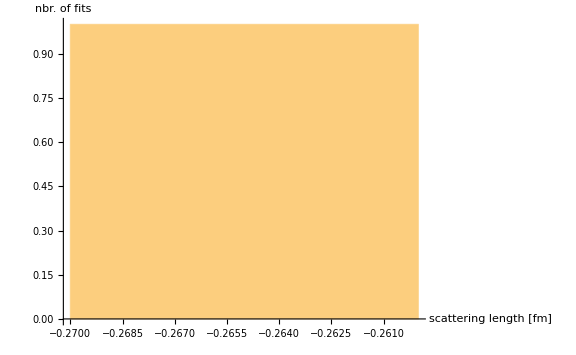

-Graphics3D-

```mathematica
cutoff=2.0;

JacobiWavefunctionPara=Select[JacobiWavefunctions,#[[1]]==cutoff&][[1]][[2]];
Rmax=8;
grdPoints=42;
r1r2Range=Subdivide[Rmax,grdPoints-1];
JacobiWavefunction=Total[#[[1]] Exp[-#[[2]] r1^2-#[[3]] r2^2]&/@JacobiWavefunctionPara];
JacobiWavefunction=JacobiWavefunction;

JacobiWavefunctionSym=Total[#[[1]] (Exp[-#[[2]] r1^2-#[[3]] r2^2]+Exp[-#[[2]] r2^2-#[[3]] r1^2])&/@JacobiWavefunctionPara];
JacobiWavefunctionGrid=Table[JacobiWavefunction/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobiWavefunctionSymGrid=Table[JacobiWavefunctionSym/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobilWavefunctionGridFlat=Flatten[Table[{R1,R2,JacobiWavefunctionSym/.{r1->R1,r2->R2}},{R1,r1r2Range},{R2,r1r2Range}],1];
fitfunctions={};
fits={};
scattlengths={};
fitDim=3;
nGrd=10;
nIter=1;
Do[
rMax=RandomReal[{10,10.1}];
Subscript[a, min]=RandomReal[{-1120,-1110}];
Subscript[a, max]=RandomReal[{1110.5,1160.10}];
Subscript[b, min]=RandomReal[{1.2,2.6}];
Subscript[b, max]=RandomReal[{40.07,120.10}];
{tmpCore,tmpFit}=FitCoreToGauss[fitDim,JacobilWavefunctionGridFlat,Subscript[a, min],Subscript[a, max],Subscript[b, min],Subscript[b, max]];
AppendTo[fitfunctions,tmpCore];
AppendTo[fits,tmpFit];
tmp=GetERE[cutoff,rMax,nGrd,tmpCore];

AppendTo[scattlengths,tmp[[1]]];

Print[nn,") a_(trimer - trimer) = ",scattlengths[[-1]],tmpCore]
,{nn,Range[nIter]}]
Histogram[scattlengths,{0.01},AxesLabel->{"scattering length [fm]","nbr. of fits"},PlotRange->{{Mean[scattlengths]-2 StandardDeviation[scattlengths],Mean[scattlengths]+2 StandardDeviation[scattlengths]},Automatic},ImageSize->Large]
selection=Range[nIter];
legends=Append[selection,"ψ_variational"];
fitsGrid=Table[Normal[#]/.{rrel1->R1,rrel2->R2},{R1,r1r2Range},{R2,r1r2Range}]&/@fits[[selection]];
ListPlot3D[Append[fitsGrid,JacobiWavefunctionGrid],PlotRange->Full,PlotLegends->legends,AxesLabel->{"|(ρ⃗)_1|  [fm]","|(ρ⃗)_2|  [fm]","∑a_n^(fit)·e^(-SubsuperscriptBox[b, n, (fit)] (SubsuperscriptBox[ρ, 1, 2] + SubsuperscriptBox[ρ, 2, 2]))"},ImageSize->Large]
```

```mathematica
selection={1};
legends=Append[selection,"ψ_variational"];
fitsGrid=Table[Normal[#]/.{rrel1->R1,rrel2->R2},{R1,r1r2Range},{R2,r1r2Range}]&/@fits[[selection]];
ListPlot3D[Append[fitsGrid,JacobiWavefunctionGrid],PlotRange->Full,PlotLegends->legends,AxesLabel->{"|(ρ⃗)_1|  [fm]","|(ρ⃗)_2|  [fm]","∑a_n^(fit)·e^(-SubsuperscriptBox[b, n, (fit)] (SubsuperscriptBox[ρ, 1, 2] + SubsuperscriptBox[ρ, 2, 2]))"},ImageSize->Large]
```

-Graphics3D-

symmetry of the wave function:
first, and foremost, I must not succumb to the fallacy of confusing rotational symmetry of a S-wave state, i.e., L_total=[[[[l_1⊗l_2]^l_12⊗l_3]^(l_((12)3))⊗l_4]^(l_(((12)3)4))⊗...]^L_total , with permutation symmetry.
In principle, the variational wave function is not guaranteed to be symmetric wrt. ρ_1↔ρ_2 interchange. The variational code obtains its optimal solution by anti-symmetrizing the total wave function,
which means that as long as the number of particles is less than the number of fermionic species, A<N_F, with N_F=4 for the two nuclear degrees of freedom, a totally anti-symmetric internal spin-isospin
wave function allows for a totally symmetric -- now wrt. any 𝔓(ermutation)∈𝔖_A(ymmetric group) -- spatial wave function.
The expansion coefficients in combination with a certain pair (for A=3) of width parameters (γ_i^(1,2)) does not reflect this symmetry explicitly if we choose different numerical values for γ_i^(1) and γ_i^(2)
ψ=𝔄^-[ Ξ⊗∑c_i·e^(-γ_i^(1)ρ_1^2)e^(-γ_i^(2)ρ_2^2) ]
Hence, we must adapt our cluster basis to 𝔄^+[∑c_i·e^(-γ_i^(1)ρ_1^2)e^(-γ_i^(2)ρ_2^2) ], i.e., the symmetrized spatial wave function.
ECCE:
i)  if a large set of widths was chosen, the symmetrization might already be realized (see examples below);
ii) (r̄)_1^2+(r̄)_2^2+(r̄)_3^2=(ρ⃗)_1^2+(ρ⃗)_2^2 (see coordinate_trafos.nb);

```mathematica
JacobiWavefunctionSymGrid//MatrixForm;
JacobiWavefunctionGrid//MatrixForm
```

(-2242. | -2049.06 | -1822.28 | -1678.57 | -1520.75 | -1323.79 | -1122.84 | -944.678 | -791.379 | -656.449 | -535.04 | -425.574
-2093.3 | -1934.86 | -1705.52 | -1537.12 | -1369.82 | -1181.18 | -997.664 | -838.17 | -701.954 | -582.269 | -474.543 | -377.367
-1687.08 | -1580.4 | -1386.05 | -1222.19 | -1070.3 | -915.364 | -771.527 | -647.862 | -542.165 | -449.299 | -365.923 | -290.955
-1211.75 | -1155.98 | -1043.29 | -933.462 | -824.126 | -712.692 | -608.256 | -515.861 | -434.56 | -361.797 | -295.899 | -236.426
-893.612 | -869.208 | -812.241 | -742.952 | -665.803 | -585.668 | -508.991 | -438.601 | -374.18 | -314.691 | -259.65 | -209.288
-708.849 | -696.098 | -662.029 | -613.911 | -557.293 | -497.749 | -439.418 | -383.848 | -331.043 | -280.818 | -233.419 | -189.518
-581.739 | -573.534 | -550.482 | -516.136 | -474.505 | -429.461 | -383.611 | -338.146 | -293.527 | -250.191 | -208.821 | -170.289
-487.002 | -481.264 | -464.952 | -439.998 | -408.719 | -373.41 | -335.882 | -297.37 | -258.761 | -220.883 | -184.619 | -150.861
-413.596 | -409.293 | -397.016 | -377.832 | -353.021 | -323.998 | -292.198 | -258.915 | -225.249 | -192.18 | -160.605 | -131.328
-351.467 | -347.999 | -338.106 | -322.42 | -301.763 | -277.197 | -249.957 | -221.28 | -192.264 | -163.85 | -136.845 | -111.919
-294.541 | -291.632 | -283.36 | -270.148 | -252.67 | -231.879 | -208.853 | -184.666 | -160.269 | -136.47 | -113.939 | -93.2128
-241.466 | -239.019 | -232.101 | -221.024 | -206.413 | -189.177 | -170.229 | -150.423 | -130.51 | -111.131 | -92.8163 | -75.9903)

```mathematica
ii=2;
JacobiWavefunctionFit=Total[#[[1]] Exp[-#[[2]] (r1^2+ r2^2+(r1+r2)^2)]&/@fitfunctions[[ii]]]
1/Sqrt[NormTF[fitfunctions[[ii]]]]
norma=NIntegrate[(*r1^2 r2^2*) JacobiWavefunctionFit*JacobiWavefunctionFit,{r1,-120,120},{r2,-120,120}]
```

-496.087 ⅇ^(-2.55877 (r1^2+r2^2+(r1+r2)^2))

1/(√NormTF[{{-99.2173,2.55877},{-99.2173,2.55877},{-99.2173,2.55877},{-99.2173,2.55877},{-99.2173,2.55877}}])

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.189618

```mathematica
NIntegrate[JacobiWavefunction*JacobiWavefunction,{r1,0,200},{r2,0,200}]
```

1.22276×10^7

```mathematica
ListPlot3D[{JacobiWavefunctionGrid},PlotLegends->{"ψ","𝔄^+ψ"},PlotRange->Full]
```

-Graphics3D-

open issues:
i)  sign of the wave function must not (?) affect observables, in general, the scattering lengths, in particular.
ii)

```mathematica
mat[N_]:=Table[If[row==col,2 "(2α)",1 "(2α)"],{row,1,N-1},{col,1,N-1}]
Do[
Print[nn,") ",mat[nn]//MatrixForm,"  |A|=",Det[mat[nn]]];
,{nn,1,10}];
```

Det::matsq: Argument {} at position 1 is not a non-empty square matrix.

1) {}  |A|=Det[{}]

2) (2 (2α))  |A|=2 (2α)

3) (2 (2α) | (2α)
(2α) | 2 (2α))  |A|=3 (2α)^2

4) (2 (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α)
(2α) | (2α) | 2 (2α))  |A|=4 (2α)^3

5) (2 (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α))  |A|=5 (2α)^4

6) (2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=6 (2α)^5

7) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=7 (2α)^6

8) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=8 (2α)^7

9) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=9 (2α)^8

10) (2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α) | (2α)
(2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | (2α) | 2 (2α))  |A|=10 (2α)^9

```mathematica
NormTF[testcore]/(1/√(NormT[testcore]^2))
```

√(NormT[testcore]^2) NormTF[testcore]

```mathematica
bnd=20;
testcore={{13.3,1.5},{103.3,2.5}};
unfi=testcore;
NormT[core_,N_:3]:=Total[Table[core[[ii]][[1]] core[[jj]][[1]] (Pi^(N-1)/(N (core[[ii]][[2]]+core[[jj]][[2]])^(N-1)))^(3/2),{ii,1,Length[core]},{jj,1,Length[core]}],2]
no=NormT[unfi];
(*Print["---------------------"]
Print["Norm=",no]
Print["---------------------"]
nfifu={#[[1]]/√no,#[[2]]}&/@unfi;
Print["Normalized: "];
nofi=1/(√no) Total[#[[1]] Exp[-#[[2]] (2 r1^2+2 r2^2+2 (r1 r2))]&/@unfi]
numi1=NIntegrate[(2 Pi)^2 r1^2 r2^2 nofi*nofi,{r1,0,bnd},{r2,0,bnd}]
*)
Print["---------------------"]
Print["Unnormalized: "];
unofi=Total[#[[1]] Exp[-#[[2]] (2 (rx1^2+ry1^2+rz1^2)+2 (rx2^2+ry2^2+rz2^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2))]&/@unfi]
numi2=NIntegrate[unofi*unofi,{rx1,-bnd,bnd},{rx2,-bnd,bnd},{ry1,-bnd,bnd},{ry2,-bnd,bnd},{rz1,-bnd,bnd},{rz2,-bnd,bnd}];
Print["∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = ",numi2,"=^?",no]
NormTF[testcore]/(1/√(NormT[testcore]^2))
Print["---------------------"]
```

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

84.4714

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------

---------------------

Unnormalized:

103.3 ⅇ^(-2.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))+13.3 ⅇ^(-1.5 (2 (rx1^2+ry1^2+rz1^2)+2 (rx1 rx2+ry1 ry2+rz1 rz2)+2 (rx2^2+ry2^2+rz2^2)))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.023 and 2.82979 for the integral and error estimates.

∫_0^(2  π) dϕ∫_-1^1 d(cosθ)∫ρ^2dρ Ψ^*Ψ = 805.023=^?804.688

804.688 NormTF[{{13.3,1.5},{103.3,2.5}}]

---------------------